```mathematica
a_⊗b_ := KroneckerProduct[a,b];
```

# Circuit Definitions

## States

```mathematica
s0ket = {{1},{0}};
s1ket = {{0},{1}};
s0bra = ConjugateTranspose[s0ket];
s1bra = ConjugateTranspose[s1ket];
```

## Single Qubit Gates

```mathematica
Id = IdentityMatrix[2];
R[θ_, ϕ_] := {{Cos[θ/2], - I Exp[-I ϕ] Sin[θ/2]},{- I Exp[I ϕ] Sin[θ/2], Cos[θ/2]}} (* Arbitrary rotaiton around the bloch sphere *)
Rx[θ_] := R[θ, 0]
Ry[θ_] := R[θ, π/2]
```

## Two Qubit Gates

```mathematica
XX[Χ_] := {{Cos[Χ], 0, 0, -I Sin[Χ]},{0, Cos[Χ], -I Sin[Χ], 0},{0, -I Sin[Χ], Cos[Χ], 0}, {- I Sin[Χ], 0, 0, Cos[Χ]}}
UMS[ϕ_] := 1/(√2){{1, 0, 0, -I Exp[-2I ϕ]},{0, 1, - I, 0},{0, -I, 1, 0},{-I Exp[2 I ϕ], 0, 0, 1}}
```

```mathematica
CZ[v1_, v2_] := (Ry[v1 π/2]⊗ Ry[v2 π/2]) XX[π/4] (Rx[-v2 π/2]⊗ Rx[-v1 π/2])(Ry[-v1 π/2]⊗ Ry[-v2 π/2])
```

```mathematica
(Ry[π/2]⊗ Ry[ π/2])
```

{{1/2,-ⅈ/2,-ⅈ/2,-1/2},{ⅈ/2,1/2,1/2,-ⅈ/2},{ⅈ/2,1/2,1/2,-ⅈ/2},{-1/2,ⅈ/2,ⅈ/2,1/2}}

```mathematica
CZ[1, 1]//N
```

{{0.0883883,0.,0.,0.+0.0883883 ⅈ},{0.,0.0883883,0.+0.0883883 ⅈ,0.},{0.,0.+0.0883883 ⅈ,0.0883883,0.},{0.+0.0883883 ⅈ,0.,0.,0.0883883}}

```mathematica
CNOT[v1_, s1_] := (Ry[v1 π/2]⊗ Id).XX[s1 π/4] .(Rx[-s1 π/2]⊗Rx[-v1 s1 π/2]) .(Ry[ -v1 π/2]⊗ Id)
```

```mathematica
CNOT[1, -1]
```

{{0,(1-ⅈ)/(√2),0,0},{(1-ⅈ)/(√2),0,0,0},{0,0,(1-ⅈ)/(√2),0},{0,0,0,(1-ⅈ)/(√2)}}

## ProjectQ Optimisation

```mathematica
circuit1[x1_, x2_] :=(Ry[x1]⊗Ry[-π/2]).CZ[1,0].(Id⊗Ry[π/2]).(Id⊗Rx[x2])
circuit2[x1_, x2_] :=(Ry[π/2+ x1]⊗Id).XX[π/4].(Rx[-π/2]⊗Id).(Ry[-π/2]⊗Rx[x2 - π/2])
circuitProjectQ = (Ry[(3π)/2]⊗Ry[2π]).UMS[0].(Ry[(3π)/2]⊗Id).(Ry[(3π)/2]⊗Rx[3 π/2]).(Id⊗Ry[2π]).(Id⊗Ry[π])
```

{{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{-ⅈ/(√2),0,-ⅈ/(√2),0},{0,ⅈ/(√2),0,ⅈ/(√2)}}

```mathematica
circuit1[π, π]
circuit2[π, π]
```

{{0,0,0,ⅈ/4},{0,0,ⅈ/4,0},{0,-ⅈ/4,0,0},{-ⅈ/4,0,0,0}}

{{0,0,0,-(1-ⅈ)/(√2)},{0,0,-(1-ⅈ)/(√2),0},{(1-ⅈ)/(√2),0,0,0},{0,(1-ⅈ)/(√2),0,0}}

## Calibration Circuit

```mathematica
calibcircuitZ0[θ1_, θ2_]:=(Ry[θ1]⊗ Id).UMS[0].(Ry[-π/2]⊗ Id).(Rx[-π/2]⊗Id).(Ry[-π/2]⊗Rx[θ2]).UMS[0].(Id⊗Ry[π/2 ])
calibcircuitX0X1[θ1_, θ2_]:=(Ry[θ1]⊗ Id).UMS[0].(Rx[π/2]⊗Rx[-π/2]).(Id⊗Ry[θ2])
```

```mathematica
θ1gs = π/2;
θ2gs = 1.796361996
initialstate = (s0ket) ⊗ (s0ket ) ;
result = calibcircuit[θgs].initialstate
result = calibcircuitX0X1[θ2gs, θ1gs].initialstate
nobright = Abs[result⟦1⟧⟦1⟧]^2
onebright = Abs[result⟦2⟧⟦1⟧]^2 + Abs[result⟦3⟧⟦1⟧]^2
twobright = Abs[result⟦4⟧⟦1⟧]^2
```

1.79636

calibcircuit[θgs].{{1},{0},{0},{0}}

{{-0.0795805+0.702614 ⅈ},{0.+0. ⅈ},{0.702614+0.0795805 ⅈ},{0.+0. ⅈ}}

0.5

0.5

0.

## MS phase offset

```mathematica
UMS[ϕ_] := 1/(√2){{1, 0, 0, I Exp[- 2 I 0]},{0, 1, - I, 0},{0, - I, 1, 0}, {I Exp[2 I ϕ], 0, 0, 1}};
(*UMS[ϕ_] := 1/(√2){{1, 0, 0, -I },{0, 1, I, 0},{0, I, 1, 0}, {-I , 0, 0, 1}};*)
R[ϕ_] := 1/(√2){{1, - I Exp[- I ϕ]},{- I Exp[I ϕ], 1}}
```

{{1/(√2)},{0},{0},{-ⅈ/(√2)}}

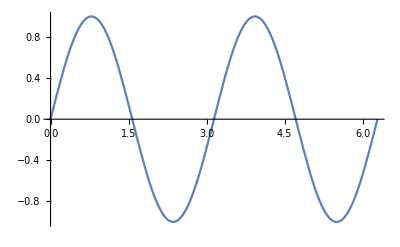

```mathematica
initialstate = (s0ket) ⊗ (s0ket ) ;
UMS[π/2]. initialstate
parity[ϕ_] := (R[ϕ]⊗R[ϕ]).UMS[π/2]. initialstate; 
(*parity[ϕ_] := (R[ϕ]⊗R[ϕ]).(1/2(s0ket ⊗s0ket + Exp[- I π/2 ]s1ket⊗s1ket)); *)
Plot[Abs[parity[ϕ]⟦1⟧⟦1⟧]^2  + Abs[parity[ϕ]⟦4⟧⟦1⟧]^2 - Abs[parity[ϕ]⟦2⟧⟦1⟧]^2  - Abs[parity[ϕ]⟦3⟧⟦1⟧]^2  , {ϕ, 0, 2 π}]
```

{{1/(√2)},{0},{0},{ⅇ^ⅈ/(√2)}}

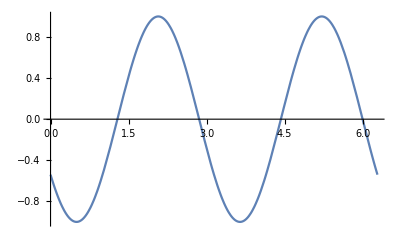

{1/(2 √2)-ⅇ^ⅈ/(2 √2)}

```mathematica
initialstate = {{1/(√2)},{0},{0},{Exp[I 1] 1/(√2)}}
parity[ϕ_] := (R[ϕ]⊗R[ϕ]). initialstate ;
Plot[Abs[parity[ϕ]⟦1⟧⟦1⟧]^2  + Abs[parity[ϕ]⟦4⟧⟦1⟧]^2 - 2 Abs[parity[ϕ]⟦2⟧⟦1⟧]^2  , {ϕ, 0, 2 π}]
parity[0]⟦1⟧
```

## MS CNOT Phase Optimisation

```mathematica
UMS[ϕ1_, ϕ2_] := 1/(√2){{1, 0, 0, -I Exp[-I (ϕ1 + ϕ2)]},{0, 1, -I Exp[- I (ϕ1 - ϕ2)], 0},{0,  -I Exp[I (ϕ1 - ϕ2)], 1 , 0},{-I Exp[I(ϕ1 + ϕ2)], 0, 0, 1}}
CNOT[ϕ_, ϕ0_, Δϕ_] := (Ry[-π/2]⊗ Id).UMS[ϕ0 , ϕ0 + Δϕ + ϕ] .(Rx[-π/2]⊗Rx[-π/2]) .(Ry[ π/2]⊗ Id)
```

```mathematica
initialstate = (s0ket) ⊗ (s0ket ) 
ProbsCNOT[ϕ_, ϕ0_, Δϕ_] := Module[{ket},
ket = CNOT[ϕ, ϕ0, Δϕ]. initialstate;
{Abs[ket⟦1⟧⟦1⟧]^2, Abs[ket⟦2⟧⟦1⟧]^2+Abs[ket⟦3⟧⟦1⟧]^2,Abs[ket⟦4⟧⟦1⟧]^2}];
ProbsCNOT[ϕ1, ϕ01, Δϕ1]
```

{{1},{0},{0},{0}}

{Abs[((1/4+ⅈ/4)+1/4 ⅇ^(ⅈ (-Δϕ1-ϕ1))+1/4 ⅈ ⅇ^(-ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)+((1/4+ⅈ/4)+1/4 ⅈ ⅇ^(ⅈ (-Δϕ1-ϕ1))+1/4 ⅇ^(-ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)]^2,Abs[((1/4-ⅈ/4)+1/4 ⅈ ⅇ^(ⅈ (-Δϕ1-ϕ1))-1/4 ⅇ^(-ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)+((-1/4+ⅈ/4)+1/4 ⅇ^(ⅈ (-Δϕ1-ϕ1))-1/4 ⅈ ⅇ^(-ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)]^2+Abs[((-1/4+ⅈ/4)+1/4 ⅇ^(-ⅈ (-Δϕ1-ϕ1))-1/4 ⅈ ⅇ^(ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)+((-1/4+ⅈ/4)-1/4 ⅈ ⅇ^(-ⅈ (-Δϕ1-ϕ1))+1/4 ⅇ^(ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)]^2,Abs[((-1/4-ⅈ/4)-1/4 ⅇ^(-ⅈ (-Δϕ1-ϕ1))-1/4 ⅈ ⅇ^(ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)+((1/4+ⅈ/4)+1/4 ⅈ ⅇ^(-ⅈ (-Δϕ1-ϕ1))+1/4 ⅇ^(ⅈ (Δϕ1+2 ϕ01+ϕ1)))/(√2)]^2}

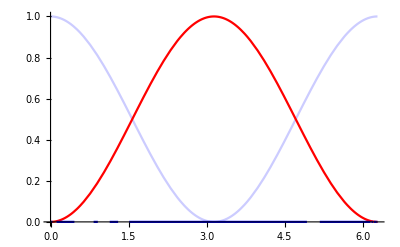

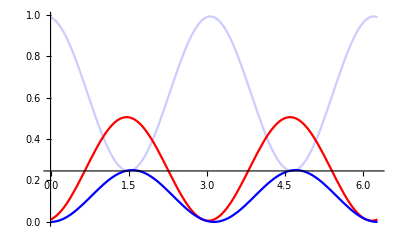

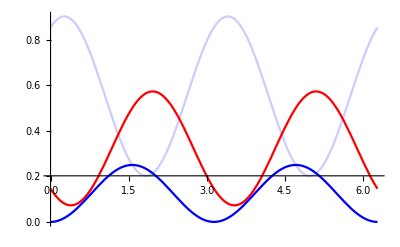

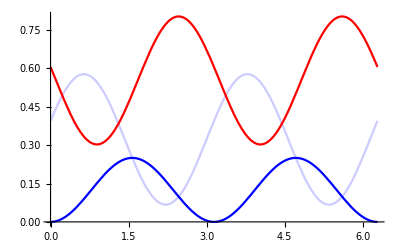

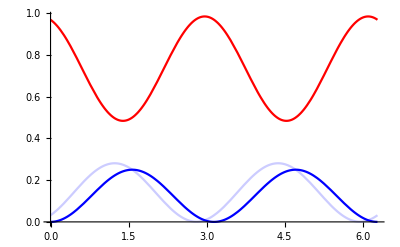

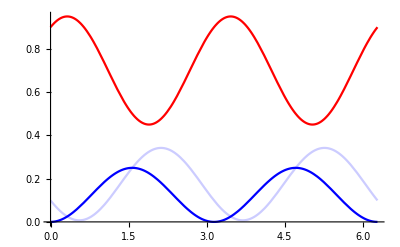

```mathematica
(**ϕ0 = π/2
Δϕ = 2.7**)
ϕ0 = 0;
Δϕ = 0;
Show[Plot[ProbsCNOT[ϕ, ϕ0,Δϕ ]⟦1⟧, {ϕ, 0, 2π}, PlotLegends-> Automatic, PlotStyle->Lighter[Blue, .8]],
Plot[ProbsCNOT[ϕ, ϕ0,Δϕ ]⟦2⟧, {ϕ, 0, 2π}, PlotLegends-> Automatic, PlotStyle->{Red}],
Plot[ProbsCNOT[ϕ, ϕ0,Δϕ ]⟦3⟧, {ϕ, 0, 2π}, PlotLegends-> Automatic, PlotStyle->{Blue}], PlotRange-> {{0, 2π},{0, 1}}, AxesOrigin->{0,0}]
```

### Fit to data

#### Data In

```mathematica
nobrightprobs = {39.8988051027102,11.794061837561202,5.1707445337785956,28.239470103171037,50.645561693891594,49.984654461076374}/100;
onebrightprobs = {27.745107101615062,35.36792562794455,51.199169427110746,58.95041637074346,45.88915348791821,29.08802473285588}/100;
twobrightprobs = {32.35608779567473,52.83801253449425,43.63008603911066,12.810113526085509,3.465284818190195,20.927320806067733}/100;
xdata = Table[i 3.14/5, {i, 0, Length[nobrightprobs] - 1}];
```

#### Function Definitions

```mathematica
CNOTnobright[ϕ_, ϕ0_, Δϕ_, A0_] := Abs[-((-1/4-ⅈ/4)-ⅇ^(-ⅈ Δϕ)/4-1/4 ⅈ ⅇ^(-ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)+((1/4+ⅈ/4)+1/4 ⅈ ⅇ^(-ⅈ Δϕ)+1/4 ⅇ^(-ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)]^2 + A0;
CNOTonebright[ϕ_, ϕ0_, Δϕ_, A0_] :=Abs[-((-1/4+ⅈ/4)+ⅇ^(-ⅈ Δϕ)/4-1/4 ⅈ ⅇ^(-ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)+((-1/4+ⅈ/4)-1/4 ⅈ ⅇ^(-ⅈ Δϕ)+1/4 ⅇ^(-ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)]^2+Abs[((1/4-ⅈ/4)+1/4 ⅈ ⅇ^(ⅈ Δϕ)-1/4 ⅇ^(ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)-((-1/4+ⅈ/4)+ⅇ^(ⅈ Δϕ)/4-1/4 ⅈ ⅇ^(ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)]^2 + A0;
CNOTtwobright[ϕ_, ϕ0_, Δϕ_, A0_] :=Abs[-((1/4+ⅈ/4)+ⅇ^(ⅈ Δϕ)/4+1/4 ⅈ ⅇ^(ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)+((1/4+ⅈ/4)+1/4 ⅈ ⅇ^(ⅈ Δϕ)+1/4 ⅇ^(ⅈ (Δϕ+2 ϕ0+2 ϕ)))/(√2)]^2 + A0;
```

#### Find Fit

```mathematica
nobrightFit = FindFit[Transpose[{xdata,nobrightprobs}], {CNOTnobright[ϕ, ϕ0var, Δϕvar, A0], 4π ≥ ϕ0var ≥ 0, 4π ≥ Δϕvar ≥ 0},{ϕ0var, Δϕvar, A0},ϕ]
onebrightFit = FindFit[Transpose[{xdata,onebrightprobs}], {CNOTonebright[ϕ, ϕ0var, Δϕvar, A0], 4π ≥ ϕ0var ≥ 0, 4π ≥ Δϕvar ≥ 0},{ϕ0var, Δϕvar, A0},ϕ]
twobrightFit = FindFit[Transpose[{xdata,twobrightprobs}], {CNOTtwobright[ϕ, ϕ0var, Δϕvar, A0], 4π ≥ ϕ0var ≥ 0, 4π ≥ Δϕvar ≥ 0},{ϕ0var, Δϕvar, A0},ϕ]
FindFit[Transpose[{xdata,nobrightprobs + onebrightprobs - twobrightprobs}], {CNOTnobright[ϕ, ϕ0var, Δϕvar, A0] + CNOTonebright[ϕ, ϕ0var, Δϕvar, A0] -CNOTtwobright[ϕ, ϕ0var, Δϕvar, A0], 4π ≥ ϕ0var ≥ 0, 4π ≥ Δϕvar ≥ 0},{ϕ0var, Δϕvar, A0},ϕ]
```

{ϕ0var→3.20946×10^-6,Δϕvar→1.43938,A0→-0.124505}

{ϕ0var→1.39209,Δϕvar→3.04641,A0→-0.297775}

{ϕ0var→0.768645,Δϕvar→1.62141,A0→0.152441}

{ϕ0var→0.768646,Δϕvar→2.46826,A0→-0.304882}

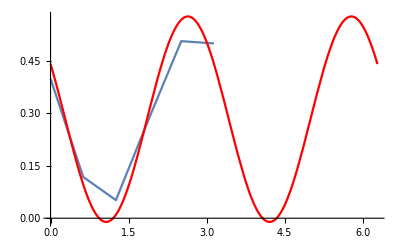

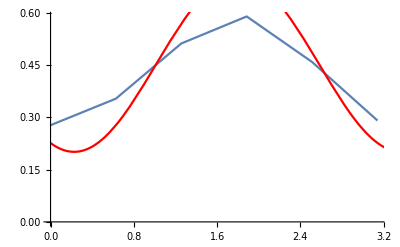

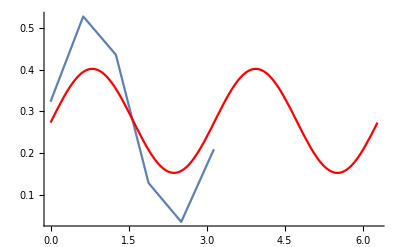

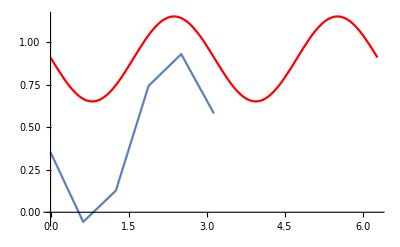

```mathematica
Show[ListLinePlot[Transpose[{xdata,nobrightprobs}]],
Plot[CNOTnobright[ϕ,ϕ0var,Δϕvar, A0]/.nobrightFit, {ϕ, 0, 2π}, PlotStyle->Red], PlotRange-> All]
Show[ListLinePlot[Transpose[{xdata,onebrightprobs}]],
Plot[CNOTonebright[ϕ,ϕ0var,Δϕvar, A0]/.onebrightFit, {ϕ, 0, 2π}, PlotStyle->Red]]
Show[ListLinePlot[Transpose[{xdata,twobrightprobs}]],
Plot[CNOTtwobright[ϕ,ϕ0var,Δϕvar, A0]/.twobrightFit, {ϕ, 0, 2π}, PlotStyle->Red], PlotRange-> All]
Show[ListLinePlot[Transpose[{xdata,nobrightprobs + onebrightprobs-twobrightprobs}]],
Plot[(CNOTnobright[ϕ, ϕ0var, Δϕvar, A0] + CNOTonebright[ϕ, ϕ0var, Δϕvar, A0] -CNOTtwobright[ϕ, ϕ0var, Δϕvar, A0])/.twobrightFit, {ϕ, 0, 2π}, PlotStyle->Red], PlotRange-> All]
```